```mathematica
Quit[]
```

```mathematica
rhosurf[r_,rcut_]:=DiracDelta[r-rcut]/(4 π rcut^2)
fsurf[r_,rcut_]:=1/(2 r rcut)(-0.28209479177387814 ⅇ^(-4. Abs[r-rcut]^2)+0.28209479177387814 ⅇ^(-4. Abs[r+rcut]^2)-Abs[r-rcut] Erf[2. Abs[r-rcut]]+Abs[r+rcut] Erf[2. Abs[r+rcut]])
```

```mathematica
(* fsurf is the LMF potential generated by rhosurf, assuming the smooth length is 0.5 *)
```

```mathematica
fG[r_,rp_,s_]:=1/(2 r rp)(Abs[r+rp] Erf[Abs[r+rp]/s] + s/Sqrt[π] Exp[-(Abs[r+rp]/s)^2] 
            - Abs[r-rp]Erf[Abs[r-rp]/s] - s/Sqrt[π] Exp[-(Abs[r-rp]/s)^2] )
(* a function useful for calculating LMF potential *)
```

```mathematica
d=0.25
ss=6
rhocorrect[r_]:=Piecewise[{{0, r<d}, {-(Erf'[(r-d)/ss]/ss)/(4π r^2), r≥d}}]
```

0.25

6

```mathematica
(* fcorrect is the correction charge density of the GT system, total correction is -1 *)
```

```mathematica
s=0.5
```

0.5

```mathematica
phi[r_?NumericQ]:=NIntegrate[rhocorrect[rp] 1/r(Abs[r+rp] Erf[Abs[r+rp]/s] + s/Sqrt[π] Exp[-(Abs[r+rp]/s)^2] 
            - Abs[r-rp]Erf[Abs[r-rp]/s] - s/Sqrt[π] Exp[-(Abs[r-rp]/s)^2] )2 π rp,{rp,0.0,20}]+fsurf[r,d]
```

```mathematica
tablephi=Table[phi[r],{r,0.01,10,0.1}]
```

{1.57457,1.54822,1.48105,1.38077,1.25801,1.1242,0.989628,0.86216,0.746753,0.645658,0.559061,0.485851,0.424296,0.372526,0.328804,0.291731,0.259848,0.232439,0.208656,0.187895,0.169672,0.153599,0.139359,0.126694,0.11539,0.105266,0.0961741,0.0879861,0.0805944,0.0739064,0.0678428,0.0623348,0.0573228,0.0527549,0.0485855,0.0447747,0.0412872,0.038092,0.0351613,0.0324706,0.0299979,0.0277237,0.0256304,0.0237022,0.0219248,0.0202855,0.0187727,0.0173759,0.0160855,0.014893,0.0137904,0.0127706,0.0118271,0.0109539,0.0101455,0.00939699,0.00870372,0.00806151,0.00746649,0.00691512,0.00640413,0.00593052,0.00549151,0.00508454,0.00470727,0.00435752,0.00403329,0.00373266,0.00345397,0.00319563,0.00295614,0.00273415,0.00252839,0.0023377,0.00216098,0.00199723,0.00184551,0.00170497,0.00157479,0.00145423,0.00134259,0.00123923,0.00114356,0.00105501,0.000973079,0.000897281,0.000827173,0.00076234,0.0007024,0.000646996,0.000595796,0.000548493,0.000504801,0.000464454,0.000427206,0.000392829,0.000361109,0.000331849,0.000304866,0.000279989}

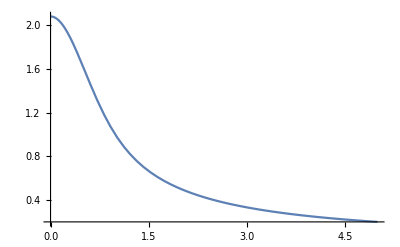

```mathematica
Plot[fsurf[r,d],{r,0,5}]
```

```mathematica
fsurf[1,d]
```

0.991449

```mathematica
interpphi=Interpolation[Transpose[{Table[r,{r,0.0001,20,0.05}],tablephi}]]
```

InterpolatingFunction[…]

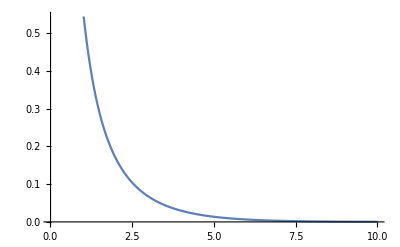

```mathematica
Plot[{interpphi[r]},{r,0.01,10}]
```

```mathematica
intphorhosurf[r_]:=NIntegrate[ phi[Sqrt[d^2+r^2-2 r d x]]/2,{x,-1,1}]
```

```mathematica
tableintrhosurf=Table[intphorhosurf[r],{r,0.1,4,0.1}]
```

NIntegrate::inumr: The integrand (2 π rp (-0.282095 ⅇ^(-4. Abs[Plus[«2»]]^2)+0.282095 ⅇ^(«1»)-«1» «1»+Abs[rp+√(0.05+Times[«2»])] Erf[2. Abs[rp+Power[«2»]]]) (Piecewise[{{0, rp<0.2}, {-ⅇ^(-1/36 Power[«2»])/(12 π^(3/2) rp^2), rp≥0.2}, {0, True}}]))/(√(0.05-0.04 x)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.1,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{0.755938,0.725961,0.679779,0.622209,0.558566,0.49377,0.431705,0.374943,0.324779,0.281497,0.244706,0.213659,0.187495,0.165381,0.146589,0.130515,0.116671,0.104669,0.0942,0.0850185,0.0769261,0.0697617,0.0633936,0.0577127,0.0526283,0.0480641,0.0439559,0.0402489,0.0368964,0.033858,0.0310993,0.0285899,0.0263038,0.0242178,0.0223119,0.0205684,0.0189714,0.0175072,0.0161632,0.0149286}

```mathematica
Erf[0.01/0.5]/0.01
```

2.25646

```mathematica
intphorhosurf[0.01]
```

1.44418

```mathematica
fsurf[0.01,d]
```

2.14171

```mathematica
Erf[0.01/0.5]/0.01+(1-1/71)^2 1.5243672271669761-(1-1/71)(fsurf[0.01,d]+phi[0.01])
```

0.0323775

```mathematica
Erf[0.01/0.5]/0.01
```

2.25646

```mathematica
(1-1/71)^2 1.5243672271669761
```

1.48173

```mathematica
(1-1/71)(fsurf[0.01,d]+phi[0.01])
```

3.70581

```mathematica
fsurf[0.01,d]
```

2.14171

```mathematica
phi[0.01]
```

1.61704

```mathematica
N[1-1/71]
```

0.985915

```mathematica
0.03*140/2.5
```

1.68

```mathematica
ϵ=71
```

71

```mathematica
final[r_]:=Erf[r/s]/r+(1-1/ϵ)^2 intphorhosurf[r]-(1-1/ϵ)(fsurf[r,d]+phi[r])
```

```mathematica
tablefinal=Table[final[r],{r,0.1,2,0.1}]
```

{0.0529947,0.0463739,0.037278,0.027785,0.0196023,0.0136269,0.00992316,0.00800397,0.00719979,0.00693279,0.00683228,0.00672324,0.0065581,0.00634799,0.00611844,0.00588964,0.00567278,0.00547188,0.0052871,0.00511705}